How to use this notebook:
	1. Run the whole section “Preliminaries” once from top to bottom. This loads the packages, sets the notebook directory, imports the χ tables and EOS GG parameter files, and defines the helper functions used everywhere else.
	2. After the setup finishes, move to the section “Calculations” and evaluate only the commands relevant to the task at hand. This section presents several examples illustrating how to use the code.
	3. To generate posterior samples for one process, use the cells in “Samples”, e.g. “GGProcessSamples[GGparams["bc"],"BD",n]”.
	4. To produce figures, use the cells in “Plots”, e.g. “PlotEOSGGfit["BD", "f+", n]”.
	5. Keep the notebook in its current folder structure: several setup cells load files through relative paths such as “chi/” and “GG_parameters/”.

Preliminaries

Packages, settings, and global variables

```mathematica
<<MaTeX`
```

```mathematica
ROR:=Identity(*options: {N, Identity}. 
This option sets whether the numerical inputs are cast in a rational form or not. 
*)
```

```mathematica
FkPo:=True(*options: {True, False}.
	Add extra fake pole to suppress Δχ contribution if True.
*)
```

```mathematica
fufa:=100(*Default 100. Increase in the constribution Δχ*)
```

```mathematica
s0N:=s0opt;
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
SetOptions[EvaluationNotebook[],CommonDefaultFormatTypes->{"Output"->TraditionalForm}]
```

```mathematica
$Assumptions={{M,m,r}∈PositiveReals,M>m};
```

```mathematica
{myGreen,myBlue,myMagenta,myOrange,myYellow}={RGBColor[0/255,200/255,120/255],RGBColor[70/255,45/255,255/255],RGBColor[220/255,0/255,157/255],RGBColor[255/255,50/255,0/255],RGBColor[210/255,230/255,0/255]}
```

{RGBColor[0, Rational[40, 51], Rational[8, 17]],RGBColor[Rational[14, 51], Rational[3, 17], 1],RGBColor[Rational[44, 51], 0, Rational[157, 255]],RGBColor[1, Rational[10, 51], 0],RGBColor[Rational[14, 17], Rational[46, 51], 0]}

References

[1] Boyd G., Grinstein B., Lebed R. (1997) 9705252 - Precision Correction to Dispersive Bounds on Form Factors
[2] Bigi D., Gambino P., Schacht S. (2017) 1707.09509 - R(Dstar), Vcb and the Heavy Quark Symmetry relations between form factors
[3] Gambino P., Jung M., Schacht S. (2019) 1905.08209 - The Vcb puzzle, an update
[4] Parrott W., Bouchard C., Davies C. (2022) 2207.12468 - B to K and D to K form factors from fully relativistic lattice QCD
[5] 102 NG240424UB2 generateFFvalues
[6] Gubernari N., Reboud M.,  van Dyk D., Virto J. (2023) 2305.06301 - Dispersive Analysis of B to K(star) and Bs to phi Form Factors
[7] Lellouch L. (1995) 9509358 - Lattice-Constrained Unitarity Bounds for B to pi l nu Decays
[8] Di Carlo M. et al. (2021) 2105.02497 - Unitarity Bounds for Semileptonic Decays in Lattice QCD
[9] Martinelli G., Simula S., Vittorio L. (2021) 2105.08674 - Vcb and RD(star) using lattice QCD and unitarity
[10] Parrott W., Bouchard C., Davies C. (2022) 2207.12468 - B to K and D to K form factors from fully relativistic lattice QCD
[11] JLQCD collaboration (2023) 2306.05657 - B to Dstar l nu semileptonic form factors from lattice QCD with Mobius domain-wall quarks
[12] https://github.com/eos/eos/blob/master/eos/constraints/B-to-V-form-factors.yaml
[13] Bigi D., Gambino P., Schacht S. (2017) 1707.09509 - R(Dstar), Vcb and the Heavy Quark Symmetry relations between form factors
[14] Fermilab MILC (2021) 2105.14019 - Semileptonic form factors for B to Dstar l nu at nonzero recoil from 2+1-flavour lattice QCD
[16] https://arxiv.org/abs/2305.06301
[17] Pullin B., Zwicky R. (2021) 2106.13617 - Radiative Decays of Heavy-light Mesons and the f(T)_H,H∗,H1 Decay Constants
[18] Djouadi A., Gambino P. (1993) 9309298 - Electroweak gauge boson self-energies, complete QCD corrections
[19] Bharucha A., Feldmann T., Wick M. (2010) 1004.3249 - Theoretical and Phenomenological Constraints on FFs for Radiative and Semi-Leptonic B-Decays
[20] Bigi D., Gambino P. (2016) 1606.08030 - Revisiting B to D l nu
[22] Grigo J., Hoff J., Marquard P., Steinhauser M. (2012) 1206.3418 - Moments of heavy quark correlators with two masses, exact mass 
[24] https://arxiv.org/pdf/2509.02776
[25] https://arxiv.org/pdf/2507.03569
[27] Horgan R., Liu Z., Meinel S., Wingate M. (2015) 1501.00367 - Rare B decays using lattice QCD form factors
[28] Aoki Y. et al. (2024) 2411.04268 - FLAG Review 2024
[29] Colquhoun B. et al. (2015) 1503.05762 - B-meson decay constants, a more complete picture from full lattice QCD
[30] Lubicz V., Melis A., Simula S. (2017)1707.04529 - Masses and decay constants of Dstar(s) and Bstar(s) mesons with Nf=2+1+1 twisted mass fermions
[32] Caprini I., Lellouch L., Neubert M. (1997) 9712417 - Dispersive Bounds on the shape of B to D l nu Form Factors
[33] Gopal A., Gubernari N. (2024) 2412.04388 - Unitarity bounds with subthreshold and anomalous cuts for b-hadron decays
[34] Paper with Eduard. Put ref when available
[35] Caprini I. (2019) - Functional Analysis and Optimisation for Hadron Physics
[36] Bourrely C., Caprini I., Lellouch L. (2008) 0807.2722 - Model-independent description of B to pi l nu decays ana a determination of Vub

Functions

General

Lists of arguments and Associations

```mathematica
listbq={"bu","bs","bc"};
listMmP={"Bπ","BsK","BK","BD","BsDs"};
listMmV={"BsK*","BK*","Bsϕ","BD*","BsDs*"};
listMm=Join[listMmP,listMmV];
listΓJ={"V-0","A-0","V-1","A-1","T-1","AT-1"};
listΓJEOS={"V-0","V-1","T-1","A-0","V-1","A-1","T-1","AT-1"};
listffP={"f+","f0","fT"};
listffV={"V","A0","A1","A12","T1","T2","T23"};
listff=Join[listffP,listffV];
```

```mathematica
bqToMm = <|
"Bπ"->"bu",
"BsK"->"bu",
"BsK*"->"bu",
"BK"->"bs",
"BK*"->"bs",
"Bsϕ"->"bs",
"BD"->"bc",
"BsDs"->"bc",
"BD*"->"bc",
"BsDs*"->"bc"
|>;
```

myN and ImChop

```mathematica
myN[expr___]:=If[
ROR===Identity, 
Block[{$MaxExtraPrecision=500},N[expr,20]],
Identity[expr]
]

(*Remove imaginary parts smaller than 10^-n relative to the real part.*)
ImChop[z_,n_:10]:=With[{r=Re[z]},r+I Chop[Im[z],10^-n Abs[r]]]

(*Check relative difference between two numbers*)
relDiff[a_,b_]:=Print[Abs[a-b]/Max[Abs[a],Abs[b]]*100,"%"]
```

sΓ, s0, sm, sp

```mathematica
replspm={
sp->(M+m)^2,
sm->(M-m)^2
};

(*For χ calculations. The value should actually be the highest appearing the simultaneous analysis*)
smax[Mm_/;MemberQ[{"bu","bs","bc"},Mm]]:=Switch[
Mm,
"bu",
(M+m)^2//.replNum["BsK*"],
"bs",
(M+m)^2//.replNum["Bsϕ"],
"bc",
(M+m)^2//.replNum["BsDs*"]
]
```

```mathematica
sΓf[ff_]:=Switch[
ff,
"f+"|"f0"|"fT"|"V"|"T1",
sV,
"A0"|"A1"|"A12"|"T2"|"T23",
sA
]
```

```mathematica
(*For the χ1pt contribution. See paper for details*)
sΓbq[bq_,ΓJ_]:=Switch[
ΓJ,
"V-0"|"V-1"|"T-1",
sV//.replNum[bq],
"A-0"|"A-1"|"AT-1",
sA//.replNum[bq]
]
```

```mathematica
repls0opt={
s0->(M+m)(√M-√m)^2
};
s0opt=(M+m)(√M-√m)^2;
```

```mathematica
s0optV=sV(1-√(1-sm/sV));
s0optA=sA(1-√(1-sm/sA));
s0optΓ=sΓ(1-√(1-sm/sΓ));
```

```mathematica
replsSimp:=Join[replspm,repls0opt,{sΓ->sp}]
repls[s0R_,spR_:sp]:=Join[replspm,{s0->s0R,sΓ->spR}]
```

z mapping

```mathematica
z[q2_,s0_,sΓ_]:= (√(sΓ-q2)-√(sΓ-s0))/(√(sΓ-q2)+√(sΓ-s0))
```

```mathematica
z[q2_,s0_]:= z[q2,s0,sΓ]
```

```mathematica
z[q2_]:=z[q2,s0,sΓ]
```

```mathematica
q2z[zz_,s0_]:= (s0 (zz+1)^2-4 sΓ*zz)/(zz-1)^2
```

```mathematica
q2z[zz_]:=q2z[zz,s0]
```

```mathematica
Jacqtoz=D[q2z[zz],zz]//Simplify;
Jacztoq=D[z[q2],q2]//Simplify;
Jacztoθ=D[Exp[I*θ],θ]//.Exp[I*θ]->zz;
```

Blaschke products, MRlist, and fRlist

J^P         Γ,J
0^-         A,0
0^+        V,0
1^-        V,1
1^+         A,1

```mathematica
BPs[Mm_,ΓJ_,q2_]/;ListQ[MRlist[Mm,ΓJ]]:=
Times@@MapIndexed[
If[#<√sΓ,z[q2,#^2,sΓ],1]
&,MRlist[Mm,ΓJ]]
```

Masses values from my paper

```mathematica
MRlist["bu","A-0"]:={5279/1000}//ROR;
MRlist["bu","V-0"]:=If[FkPo===True,{5642/1000},{}]//ROR;
MRlist["bu","V-1"]:={5325/1000}//ROR;
MRlist["bu","A-1"]:={5726/1000}//ROR;
MRlist["bu","T-1"]:=MRlist["bu","V-1"];
MRlist["bu","AT-1"]:=MRlist["bu","A-1"];
```

```mathematica
MRlist["bs","A-0"]:={5367/1000}//ROR;
MRlist["bs","V-0"]:={5711/1000}//ROR;
MRlist["bs","V-1"]:={5415/1000}//ROR;
MRlist["bs","A-1"]:={5829/1000}//ROR;
MRlist["bs","T-1"]:=MRlist["bs","V-1"];
MRlist["bs","AT-1"]:=MRlist["bs","A-1"];
```

```mathematica
MRlist["bc","A-0"]:={6274/1000,6871/1000}//ROR;
MRlist["bc","V-0"]:={6707/1000}//ROR;
MRlist["bc","V-1"]:={6328/1000,6922/1000}//ROR;
MRlist["bc","A-1"]:={6739/1000}//ROR;
MRlist["bc","T-1"]:=MRlist["bc","V-1"];
MRlist["bc","AT-1"]:=MRlist["bc","A-1"];
```

Decay constants values from my paper

fRlist and MRlist must have the same length. If the decay constant is no known I put it to zero so it does not contribute to χ1pt.

```mathematica
fRlist["bu","A-0"]:={1900*10^-4(*[28]*)}//ROR;
fRlist["bu","V-0"]:=If[FkPo===True,{0(*FkPo*)},{}]//ROR;
fRlist["bu","V-1"]:={1900*10^-4*958*10^-3(*[30]*)}//ROR;
fRlist["bu","A-1"]:={2470*10^-4(*[17]*)}//ROR;
fRlist["bu","T-1"]:={2000*10^-4(*[17]*)}//ROR;
fRlist["bu","AT-1"]:={2300*10^-4(*[17]*)}//ROR;
```

```mathematica
fRlist["bs","A-0"]:={2303*10^-4(*[28]*)}//ROR;
fRlist["bs","V-0"]:={0(*Unknown*)}//ROR;
fRlist["bs","V-1"]:={2303*10^-4*974*10^-3(*[30]*)}//ROR;
fRlist["bs","A-1"]:={3050*10^-4(*[17]*)}//ROR;
fRlist["bs","T-1"]:={2360*10^-4(*[17]*)}//ROR;
fRlist["bs","AT-1"]:={2850*10^-4(*[17]*)}//ROR;
```

```mathematica
fRlist["bc","A-0"]:={4340*10^-4(*[29]*),0}//ROR;
fRlist["bc","V-0"]:={1920*10^-4(*[34]*)}//ROR;
fRlist["bc","V-1"]:={4340*10^-4*988*10^-3(*[29]*),0}//ROR;
fRlist["bc","A-1"]:={2730*10^-4(*[34]*)}//ROR;
fRlist["bc","T-1"]:={4970*10^-4(*[34]*),0}//ROR;
fRlist["bc","AT-1"]:={2310*10^-4(*[34]*)}//ROR;
```

Make _x function explicit

```mathematica
replx:={
zx->z,
ϕBGLx->ϕBGLs,
ϕGx->ϕGs,
BPx->BPs
}
```

Replace χ and BP

```mathematica
χ[Mm_,ΓJ_]:=χ[Mm,ΓJ,0,0]
χ[Mm_,ΓJ_,Q2_]:=χ[Mm,ΓJ,Q2,0]
```

```mathematica
χ["Bπ",ΓJ_,Q2_:0,e_:0]:=χ["bu",ΓJ,Q2,e]
χ["BsK",ΓJ_,Q2_:0,e_:0]:=χ["bu",ΓJ,Q2,e]
χ["BsK*",ΓJ_,Q2_:0,e_:0]:=χ["bu",ΓJ,Q2,e]
BPs["Bπ",ΓJ_,q2_]:=BPs["bu",ΓJ,q2]
BPs["BsK",ΓJ_,q2_]:=BPs["bu",ΓJ,q2]
BPs["BsK*",ΓJ_,q2_]:=BPs["bu",ΓJ,q2]
MRlist["Bπ",ΓJ_]:=MRlist["bu",ΓJ]
MRlist["BsK",ΓJ_]:=MRlist["bu",ΓJ]
MRlist["BsK*",ΓJ_]:=MRlist["bu",ΓJ]
smax["Bπ"]:=smax["bu"]
smax["BsK"]:=smax["bu"]
smax["BsK*"]:=smax["bu"]

χ["BK",ΓJ_,Q2_:0,e_:0]:=χ["bs",ΓJ,Q2,e]
χ["BK*",ΓJ_,Q2_:0,e_:0]:=χ["bs",ΓJ,Q2,e]
χ["Bsϕ",ΓJ_,Q2_:0,e_:0]:=χ["bs",ΓJ,Q2,e]
BPs["BK",ΓJ_,q2_]:=BPs["bs",ΓJ,q2]
BPs["BK*",ΓJ_,q2_]:=BPs["bs",ΓJ,q2]
BPs["Bsϕ",ΓJ_,q2_]:=BPs["bs",ΓJ,q2]
MRlist["BK",ΓJ_]:=MRlist["bs",ΓJ]
MRlist["BK*",ΓJ_]:=MRlist["bs",ΓJ]
MRlist["Bsϕ",ΓJ_]:=MRlist["bs",ΓJ]
smax["BK"]:=smax["bs"]
smax["BK*"]:=smax["bs"]
smax["Bsϕ"]:=smax["bs"]

χ["BD",ΓJ_,Q2_:0,e_:0]:=χ["bc",ΓJ,Q2,e]
χ["BsDs",ΓJ_,Q2_:0,e_:0]:=χ["bc",ΓJ,Q2,e]
χ["BD*",ΓJ_,Q2_:0,e_:0]:=χ["bc",ΓJ,Q2,e]
χ["BsDs*",ΓJ_,Q2_:0,e_:0]:=χ["bc",ΓJ,Q2,e]
BPs["BD",ΓJ_,q2_]:=BPs["bc",ΓJ,q2]
BPs["BsDs",ΓJ_,q2_]:=BPs["bc",ΓJ,q2]
BPs["BD*",ΓJ_,q2_]:=BPs["bc",ΓJ,q2]
BPs["BsDs*",ΓJ_,q2_]:=BPs["bc",ΓJ,q2]
MRlist["BD",ΓJ_]:=MRlist["bc",ΓJ]
MRlist["BsDs",ΓJ_]:=MRlist["bc",ΓJ]
MRlist["BD*",ΓJ_]:=MRlist["bc",ΓJ]
MRlist["BsDs*",ΓJ_]:=MRlist["bc",ΓJ]
smax["BD"]:=smax["bc"]
smax["BsDs"]:=smax["bc"]
smax["BD*"]:=smax["bc"]
smax["BsDs*"]:=smax["bc"]
```

```mathematica
replχBP={
χ[Mm_,"f+",Q2_:0,e_:0]:>χ[Mm,"V-1",Q2,e],
BPx[Mm_,"f+",q2_]:>BPx[Mm,"V-1",q2],
BPs[Mm_,"f+",q2_]:>BPs[Mm,"V-1",q2],
MRlist[Mm_,"f+"]:>MRlist[Mm,"V-1"],

χ[Mm_,"f0",Q2_:0,e_:0]:>χ[Mm,"V-0",Q2,e],
BPx[Mm_,"f0",q2_]:>BPx[Mm,"V-0",q2],
BPs[Mm_,"f0",q2_]:>BPs[Mm,"V-0",q2],
MRlist[Mm_,"f0"]:>MRlist[Mm,"V-0"],

χ[Mm_,"fT",Q2_:0,e_:0]:>χ[Mm,"T-1",Q2,e],
BPx[Mm_,"fT",q2_]:>BPx[Mm,"T-1",q2],
BPs[Mm_,"fT",q2_]:>BPs[Mm,"T-1",q2],
MRlist[Mm_,"fT"]:>MRlist[Mm,"T-1"],

χ[Mm_,"V",Q2_:0,e_:0]:>χ[Mm,"V-1",Q2,e],
BPx[Mm_,"V",q2_]:>BPx[Mm,"V-1",q2],
BPs[Mm_,"V",q2_]:>BPs[Mm,"V-1",q2],
MRlist[Mm_,"V"]:>MRlist[Mm,"V-1"],

χ[Mm_,"A0",Q2_:0,e_:0]:>χ[Mm,"A-0",Q2,e],
BPx[Mm_,"A0",q2_]:>BPx[Mm,"A-0",q2],
BPs[Mm_,"A0",q2_]:>BPs[Mm,"A-0",q2],
MRlist[Mm_,"A0"]:>MRlist[Mm,"A-0"],

χ[Mm_,"A1",Q2_:0,e_:0]:>χ[Mm,"A-1",Q2,e],
BPx[Mm_,"A1",q2_]:>BPx[Mm,"A-1",q2],
BPs[Mm_,"A1",q2_]:>BPs[Mm,"A-1",q2],
MRlist[Mm_,"A1"]:>MRlist[Mm,"A-1"],

χ[Mm_,"A12",Q2_:0,e_:0]:>χ[Mm,"A-1",Q2,e],
BPx[Mm_,"A12",q2_]:>BPx[Mm,"A-1",q2],
BPs[Mm_,"A12",q2_]:>BPs[Mm,"A-1",q2],
MRlist[Mm_,"A12"]:>MRlist[Mm,"A-1"],

χ[Mm_,"T1",Q2_:0,e_:0]:>χ[Mm,"T-1",Q2,e],
BPx[Mm_,"T1",q2_]:>BPx[Mm,"T-1",q2],
BPs[Mm_,"T1",q2_]:>BPs[Mm,"T-1",q2],
MRlist[Mm_,"T1"]:>MRlist[Mm,"T-1"],

χ[Mm_,"T2",Q2_:0,e_:0]:>χ[Mm,"AT-1",Q2,e],
BPx[Mm_,"T2",q2_]:>BPx[Mm,"AT-1",q2],
BPs[Mm_,"T2",q2_]:>BPs[Mm,"AT-1",q2],
MRlist[Mm_,"T2"]:>MRlist[Mm,"AT-1"],

χ[Mm_,"T23",Q2_:0,e_:0]:>χ[Mm,"AT-1",Q2,e],
BPx[Mm_,"T23",q2_]:>BPx[Mm,"AT-1",q2],
BPs[Mm_,"T23",q2_]:>BPs[Mm,"AT-1",q2],
MRlist[Mm_,"T23"]:>MRlist[Mm,"AT-1"]
};
```

Parametrizations

BGL

Outer and weight functions master formula

Eq. (4.14) of ref. [1]
sΓ=sp if the threshold coincides with (M+m)^2. Otherwise sp=(M+m)^2(which come from the weight function, i.e. the FFs definitions) and sΓ=threshold, which come from the definition of z

```mathematica
ϕBGLs[s_,K_,a_,b_,c_,d_,χ_,Q2_:0]:=√(nI/(K*π*χ))((sΓ-s)/(sΓ-s0))^(1/4)(√(sΓ-s)+√(sΓ-s0))(sp-s)^(a/4)(√(sΓ-s)+√(sΓ-sm))^(b/2)(√(sΓ-s)+√sΓ)^(-(c+3))((√(sΓ-s)+√sΓ)/(√(sΓ-s)+√(sΓ+Q2)))^d
```

Eq. (4.13) of ref. [1], to which I add  the denominator of eq. (3.2)

```mathematica
WBGL[s_,K_,a_,b_,c_,d_,Q2_:0]:=nI/(K π)Abs[(s-sp)^(a/2)(s-sm)^(b/2)] s^(-(c+3))(s/(s+Q2))^d(*The absolute value is needed for the Kallen funtionbelow s+. See [33]*)
```

Outer functions for FFs

```mathematica
ϕBGLf["f+",q2_,χ_,Q2_:0]:=ϕBGLx[q2,48,3,3,2,3,χ,Q2]
ϕBGLf["f0",q2_,χ_,Q2_:0]:=ϕBGLx[q2,1/((M^2-m^2)^2)16,1,1,1,2,χ,Q2]
ϕBGLf["fT",q2_,χ_,Q2_:0]:=ϕBGLx[q2,48(M+m)^2,3,3,1,4,χ,Q2]
ϕBGLf["V",q2_,χ_,Q2_:0]:=ϕBGLx[q2,1/2^2(M+m)^2 96,3,3,1,3,χ,Q2]
ϕBGLf["A0",q2_,χ_,Q2_:0]:=ϕBGLx[q2,1/2^2 64,3,3,1,2,χ,Q2]
ϕBGLf["A1",q2_,χ_,Q2_:0]:=ϕBGLx[q2,1/(M+m)^2 24,1,1,1,3,χ,Q2]
ϕBGLf["A12",q2_,χ_,Q2_:0]:=ϕBGLx[q2,1/(8M*m)^2 48(*==12/(sp-sm)^2*),1,1,2,3,χ,Q2]
ϕBGLf["T1",q2_,χ_,Q2_:0]:=ϕBGLx[q2,24,3,3,2,4,χ,Q2]
ϕBGLf["T2",q2_,χ_,Q2_:0]:=ϕBGLx[q2,24/((M^2-m^2)^2),1,1,2,4,χ,Q2]
ϕBGLf["T23",q2_,χ_,Q2_:0]:=ϕBGLx[q2,(3(M+m)^2)/(M^2*m^2)(*==(48sp)/(sp-sm)^2*),1,1,1,4,χ,Q2]
```

z series

```mathematica
zseries["BGL",Mm_,ff_,KK_,q2_]:=Sum[
α["BGL",Mm,ff,k] zx[q2]^k
,{k,0,KK-1}]
```

FFs

```mathematica
FF["BGL",Mm_,ff_,KK_,q2_,Q2_:0]:=1/(ϕBGLf[ff,q2,χ[Mm,ff,Q2,0],Q2]BPx[Mm,ff,q2])zseries["BGL",Mm,ff,KK,q2]//.replχBP
```

G

Outer and weight functions master formula

```mathematica
factMresϕ[s_,MRli_List,Q2_:0]:=Times@@MapIndexed[
If[√sΓ<#<√sp,((#^2-s)/(√(sΓ-s)+√(sΓ+Q2))^2),1]
&,MRli]

ϕGs[s_,K_,a_,b_,c_,d_,χ_,MRli_List,Q2_:0,e_:0]:=ϕBGLs[s,K,a,b,c+e,d+e,χ,Q2]factMresϕ[s,MRli,Q2]
```

```mathematica
factMresW[s_,MRli_List,Q2_:0]:=Times@@MapIndexed[
If[√sΓ<#<√sp,((#^2-s)/(s+Q2))^2,1]
&,MRli]
WG[s_,K_,a_,b_,c_,d_,MRli_List,Q2_:0,e_:0]:=WBGL[s,K,a,b,c+e,d+e,Q2]factMresW[s,MRli,Q2]
```

Outer and weight functions for FFs

```mathematica
ϕGf[Mm_,"f+",q2_,χ_,Q2_:0,e_:0]:=ϕGx[q2,48,3,3,2,3,χ,MRlist[Mm,"f+"],Q2,e]
ϕGf[Mm_,"f0",q2_,χ_,Q2_:0,e_:0]:=ϕGx[q2,16/(sp*sm),1,1,1,2,χ,MRlist[Mm,"f0"],Q2,e]
ϕGf[Mm_,"fT",q2_,χ_,Q2_:0,e_:0]:=ϕGx[q2,48sp,3,3,1,4,χ,MRlist[Mm,"fT"],Q2,e]
ϕGf[Mm_,"V",q2_,χ_,Q2_:0,e_:0]:=ϕGx[q2,24sp,3,3,1,3,χ,MRlist[Mm,"V"],Q2,e]
ϕGf[Mm_,"A0",q2_,χ_,Q2_:0,e_:0]:=ϕGx[q2,16,3,3,1,2,χ,MRlist[Mm,"A0"],Q2,e]
ϕGf[Mm_,"A1",q2_,χ_,Q2_:0,e_:0]:=ϕGx[q2,24/sp,1,1,1,3,χ,MRlist[Mm,"A1"],Q2,e]
ϕGf[Mm_,"A12",q2_,χ_,Q2_:0,e_:0]:=ϕGx[q2,12/(sp-sm)^2,1,1,2,3,χ,MRlist[Mm,"A12"],Q2,e]
ϕGf[Mm_,"T1",q2_,χ_,Q2_:0,e_:0]:=ϕGx[q2,24,3,3,2,4,χ,MRlist[Mm,"T1"],Q2,e]
ϕGf[Mm_,"T2",q2_,χ_,Q2_:0,e_:0]:=ϕGx[q2,24/(sp*sm),1,1,2,4,χ,MRlist[Mm,"T2"],Q2,e]
ϕGf[Mm_,"T23",q2_,χ_,Q2_:0,e_:0]:=ϕGx[q2,(48sp)/(sp-sm)^2,1,1,1,4,χ,MRlist[Mm,"T23"],Q2,e]

WGf[Mm_,"f+",q2_,Q2_:0,e_:0]:=WG[q2,48,3,3,2,3,MRlist[Mm,"f+"],Q2,e]
WGf[Mm_,"f0",q2_,Q2_:0,e_:0]:=WG[q2,16/(sp*sm),1,1,1,2,MRlist[Mm,"f0"],Q2,e]
WGf[Mm_,"fT",q2_,Q2_:0,e_:0]:=WG[q2,48sp,3,3,1,4,MRlist[Mm,"fT"],Q2,e]
WGf[Mm_,"V",q2_,Q2_:0,e_:0]:=WG[q2,24sp,3,3,1,3,MRlist[Mm,"V"],Q2,e]
WGf[Mm_,"A0",q2_,Q2_:0,e_:0]:=WG[q2,16,3,3,1,2,MRlist[Mm,"A0"],Q2,e]
WGf[Mm_,"A1",q2_,Q2_:0,e_:0]:=WG[q2,24/sp,1,1,1,3,MRlist[Mm,"A1"],Q2,e]
WGf[Mm_,"A12",q2_,Q2_:0,e_:0]:=WG[q2,12/(sp-sm)^2,1,1,2,3,MRlist[Mm,"A12"],Q2,e]
WGf[Mm_,"T1",q2_,Q2_:0,e_:0]:=WG[q2,24,3,3,2,4,MRlist[Mm,"T1"],Q2,e]
WGf[Mm_,"T2",q2_,Q2_:0,e_:0]:=WG[q2,24/(sp*sm),1,1,2,4,MRlist[Mm,"T2"],Q2,e]
WGf[Mm_,"T23",q2_,Q2_:0,e_:0]:=WG[q2,(48sp)/(sp-sm)^2,1,1,1,4,MRlist[Mm,"T23"],Q2,e]
```

z series

```mathematica
zseries["G",Mm_,ff_,KK_,q2_,startα_:0]:=Sum[
α["G",Mm,ff,k] zx[q2]^k
,{k,startα,KK-1}]
```

FFs

```mathematica
FF["G",Mm_,ff_,KK_,q2_,Q2_:0,e_:0]:=1/(ϕGf[Mm,ff,q2,χ[Mm,ff,Q2,e],Q2,e]BPx[Mm,ff,q2])zseries["G",Mm,ff,KK,q2]//.replχBP
```

Endpoint relations

```mathematica
αGE[Mm_,"f0",0,KK_,Q2_:0,e_:0]:=(ϕGf[Mm,"f0",0,χ[Mm,"f0",Q2,e],Q2,e]BPx[Mm,"f0",0])/(ϕGf[Mm,"f+",0,χ[Mm,"f+",Q2,e],Q2,e]BPx[Mm,"f+",0])zseries["G",Mm,"f+",KK,0]-zseries["G",Mm,"f0",KK,0,1(*start*)]//.replχBP
```

```mathematica
αGE[Mm_,"A12",0,KK_,Q2_:0,e_:0]:=(M^2-m^2)/(8M*m)(ϕGf[Mm,"A12",0,χ[Mm,"A12",Q2,e],Q2,e]BPx[Mm,"A12",0])/(ϕGf[Mm,"A0",0,χ[Mm,"A0",Q2,e],Q2,e]BPx[Mm,"A0",0])zseries["G",Mm,"A0",KK,0]-zseries["G",Mm,"A12",KK,0,1(*start*)]//.replχBP
```

```mathematica
αGE[Mm_,"A1",0,KK_,Q2_:0,e_:0]:=(8M*m)/(M^2-m^2)(ϕGf[Mm,"A1",sm,χ[Mm,"A1",Q2,e],Q2,e]BPx[Mm,"A1",sm])/(ϕGf[Mm,"A12",sm,χ[Mm,"A12",Q2,e],Q2,e]BPx[Mm,"A12",sm])zseries["G",Mm,"A12",KK,sm]-zseries["G",Mm,"A1",KK,sm,1(*start*)]//.replχBP
```

```mathematica
(*The implementation of this one is a bit different because it is function of both sA and sV. *)
αGE[Mm_,"T2",0,KK_,Q2_:0,e_:0]:=((ϕGf[Mm,"T2",0,χ[Mm,"T2",Q2,e],Q2,e]BPx[Mm,"T2",0]//.Join[replx,repls[s0optA,sA],replχBP])/(ϕGf[Mm,"T1",0,χ[Mm,"T1",Q2,e],Q2,e]BPx[Mm,"T1",0]//.Join[replx,repls[s0optV,sV],replχBP]))(zseries["G",Mm,"T1",KK,0]//.Join[replx,repls[s0optV,sV],replχBP])-(zseries["G",Mm,"T2",KK,0,1(*start*)]//.Join[replx,repls[s0optA,sA],replχBP])
```

```mathematica
αGE[Mm_,"T23",0,KK_,Q2_:0,e_:0]:=(M+m)^2/(4M*m)(ϕGf[Mm,"T23",sm,χ[Mm,"T23",Q2,e],Q2,e]BPx[Mm,"T23",sm])/(ϕGf[Mm,"T2",sm,χ[Mm,"T2",Q2,e],Q2,e]BPx[Mm,"T2",sm])zseries["G",Mm,"T2",KK,sm]-zseries["G",Mm,"T23",KK,sm,1(*start*)]//.replχBP
```

Construct χ

Construct χANSO (include NNLO corrections)

```mathematica
Clear[χANSnnlo]
χANSnnlo[
bq_/;MemberQ[listbq,bq],
ΓJ_/;MemberQ[{"V-0","A-0","V-1","A-1"},ΓJ],
Q2_,
e_
]/;(Q2!=0||e!=0):=0

χANSnnlo[
bq_/;MemberQ[listbq,bq],
ΓJ_/;MemberQ[{"T-1","AT-1"},ΓJ],
Q2_,
e_
]:=0

(*From [22]*)
χANSnnlo["bu","A-0",0,0]=0.00026299616726318636;
χANSnnlo["bu","V-0",0,0]=0.00026299616726318636;
χANSnnlo["bu","V-1",0,0]=-8.016172866100229*^-7;
χANSnnlo["bu","A-1",0,0]=-8.016172866100229*^-7;

χANSnnlo["bu","A-0",0,1]=0.000011712968296883236;
χANSnnlo["bu","V-0",0,1]=0.000011712968296883236;
χANSnnlo["bu","V-1",0,1]=-4.1041516400088015*^-8;
χANSnnlo["bu","A-1",0,1]=-4.1041516400088015*^-8;

χANSnnlo["bu","A-0",0,2]=2.555554604506779*^-7;
χANSnnlo["bu","V-0",0,2]=2.555554604506779*^-7;
χANSnnlo["bu","V-1",0,2]=-2.7663813113130346*^-9;
χANSnnlo["bu","A-1",0,2]=-2.7663813113130346*^-9;

χANSnnlo["bs","A-0",0,0]=0.00035558949714692005;
χANSnnlo["bs","V-0",0,0]=0.00017012383028357464;
χANSnnlo["bs","V-1",0,0]=1.6120479888663802*^-6;
χANSnnlo["bs","A-1",0,0]=-3.3516815015700703*^-6;

χANSnnlo["bs","A-0",0,1]=0.0000147318388386161;
χANSnnlo["bs","V-0",0,1]=8.617824279469381*^-6;
χANSnnlo["bs","V-1",0,1]=2.9705559022459164*^-8;
χANSnnlo["bs","A-1",0,1]=-1.1758780487088253*^-7;

χANSnnlo["bs","A-0",0,2]=3.470118716066278*^-7;
χANSnnlo["bs","V-0",0,2]=1.5932436358662233*^-7;
χANSnnlo["bs","V-1",0,2]=-6.252000149419089*^-10;
χANSnnlo["bs","A-1",0,2]=-5.142307419380408*^-9;

χANSnnlo["bc","A-0",0,0]=0.0006389447491015023;
χANSnnlo["bc","V-0",0,0]=-0.0001452172501779895;
χANSnnlo["bc","V-1",0,0]=4.255189319879084*^-6;
χANSnnlo["bc","A-1",0,0]=-9.102016877578465*^-6;

χANSnnlo["bc","A-0",0,1]=0.000020378788637639202;
χANSnnlo["bc","V-0",0,1]=-6.205295245623964*^-7;
χANSnnlo["bc","V-1",0,1]=3.291716363403299*^-8;
χANSnnlo["bc","A-1",0,1]=-1.7602078117974395*^-7;

χANSnnlo["bc","A-0",0,2]=3.8284318896566936*^-7;
χANSnnlo["bc","V-0",0,2]=-2.8843972118648978*^-8;
χANSnnlo["bc","V-1",0,2]=-1.6010695700508665*^-9;
χANSnnlo["bc","A-1",0,2]=-3.828004355929786*^-9;
```

```mathematica
Clear[χANSO]
χANSO[bq_/;MemberQ[listbq,bq],
ΓJ_/;MemberQ[{"V-0","A-0","V-1","A-1","T-1","AT-1"},ΓJ],
Q2_,
e_]:=χANS[bq,ΓJ,Q2,e]+χANSnnlo[bq,ΓJ,Q2,e]
```

```mathematica
Clear[hχANSO]
hχANSO[
bq_/;MemberQ[listbq,bq],
ΓJ_/;MemberQ[listΓJ,ΓJ],
Q2_(*:0*),
e_(*:0*)
]:=(**)Module[{MRinside},
(*Select states are in the interval [sΓ,sp]*)
MRinside=Select[MRlist[bq,ΓJ],√sΓbq[bq,ΓJ]<#<√smax[bq]&];

Switch[
Length[MRinside],
0,
χANSO[bq,ΓJ,Q2,e],
1,
χANSO[bq,ΓJ,Q2,e]-2(First[MRinside]^2+Q2)χANSO[bq,ΓJ,Q2,e+1]+(First[MRinside]^2+Q2)^2 χANSO[bq,ΓJ,Q2,e+2],
_,
Message[hχANSO::many,Length[MRinside]];
$Failed
]

]
hχANSO::many="There are `1` states inside the interval. The procedure is implemented only for 0 and 1.";
```

Construct χ1pt

Implementation not valid for BGL with sΓ!=sp (I put  #1 < Sqrt[sp])

```mathematica
χ1pt[
bq_/;MemberQ[listbq,bq],
ΓJ_/;MemberQ[listΓJ,ΓJ],
Q2_(*:0*),
e_(*:0*)
]:=Module[{kN,pMR,subN,res},

(*Use minimal number of subtractions if unspecified*)
{kN,pMR}=Switch[
ΓJ,
"V-0"|"A-0",
{1,2},
"V-1"|"A-1",
{2,2},
"T-1"|"AT-1",
{3,4}
];

subN=kN+e;

res=Total@MapThread[
If[#1<√sp,
(#1^pMR*#2^2)/((#1^2+Q2)^(subN+1)),0]
&,{MRlist[bq,ΓJ],fRlist[bq,ΓJ]}]//.sp->smax[bq];

res
]
```

```mathematica
hχ1pt[
bq_/;MemberQ[listbq,bq],
ΓJ_/;MemberQ[listΓJ,ΓJ],
Q2_(*:0*),
e_(*:0*)
]:=Module[{kN,pMR,subN,res},

(*Use minimal number of subtractions if unspecified*)
{kN,pMR}=Switch[
ΓJ,
"V-0"|"A-0",
{1,2},
"V-1"|"A-1",
{2,2},
"T-1"|"AT-1",
{3,4}
];

subN=kN+e;

res=Total@MapThread[
If[#1<√sΓ,
(#1^pMR*#2^2)/((#1^2+Q2)^(subN+1))factMresW[#1^2,MRlist[bq,ΓJ],Q2],0]
&,{MRlist[bq,ΓJ],fRlist[bq,ΓJ]}]//.{sΓ->sΓbq[bq,ΓJ],sp->smax[bq]};

res
]

χ1pt::len="fRlist and MRlist must have the same length";
```

Construct X

```mathematica
χANS1ptBGL[
bq_/;MemberQ[listbq,bq],
ΓJ_/;MemberQ[listΓJ,ΓJ],
Q2_,
e_
]:=χANS[bq,ΓJ,Q2,e]-χ1pt[bq,ΓJ,Q2,e]
```

```mathematica
XANS[
bq_/;MemberQ[listbq,bq],
ΓJ_/;MemberQ[listΓJ,ΓJ],
Q2_,
e_,
fudgefa_:fufa
]:=hχANS[bq,ΓJ,Q2,e]-hχ1pt[bq,ΓJ,Q2,e]+fudgefa*hΔχS[bq,ΓJ,Q2,e](*see Eq. (8) of [32] and Eq. (13) of [33]*)
```

```mathematica
XANSO[
bq_/;MemberQ[listbq,bq],
ΓJ_/;MemberQ[listΓJ,ΓJ],
Q2_,
e_,
fudgefa_:fufa
]:=hχANSO[bq,ΓJ,Q2,e]-hχ1pt[bq,ΓJ,Q2,e]+fudgefa*hΔχS[bq,ΓJ,Q2,e](*see Eq. (8) of [32] and Eq. (13) of [33]*)
```

```mathematica
inc=1;
XANSinc[
bq_/;MemberQ[listbq,bq],
ΓJ_/;MemberQ[listΓJ,ΓJ],
Q2_,
e_,
fudgefa_:fufa
]:=inc*XANS[bq,ΓJ,Q2,e,fudgefa]
```

Load χANS, hχANS, and hΔχS

```mathematica
Check[
Get[Directory[]<>"//chi//chiANS.wl"];
Get[Directory[]<>"//chi//hchiANS.wl"];
Get[Directory[]<>"//chi//hDeltachiS.wl"];,
Beep[];
MessageDialog["Failed to load chi values"];
$Failed]
```

Loading and sampling EOS fit GG parameters

EOS process names to Mm

```mathematica
GGMmToEOSProcess = <|
  "Bπ" -> "B->pi",
  "BsK" -> "B_s->K",
  "BK" -> "B->K",
  "BD" -> "B->D",
  "BsDs" -> "B_s->D_s",
  "BsK*" -> "B_s->K^*",
  "BK*" -> "B->K^*",
  "Bsϕ" -> "B_s->phi",
  "BD*" -> "B->D^*",
  "BsDs*" -> "B_s->D_s^*"
|>;

GGEOSProcessToMm = Association @ Map[Reverse, Normal[GGMmToEOSProcess]];

GGCanonicalProcessKey[MTom_String] := Lookup[GGEOSProcessToMm, MTom, MTom];

GGDependentAlpha0FFs = Association @ Join[
  Rule[#, {"f0"}] & /@ {"Bπ", "BsK", "BK", "BD", "BsDs"},
  Rule[#, {"A1", "A12", "T2", "T23"}] & /@ {"BsK*", "BK*", "Bsϕ", "BD*", "BsDs*"}
];
```

Get FF parameters info and position

```mathematica
(*It parses one EOS parameter name string and turns it into structured information, e.g.
  In: GGParseParameterName["B->K::a^f+_0@G2026"] 
Out: <|"ProcessEOS"->"B->K","Mm"->"BK","ff"->"f+","k"->0|>
*)
GGParseParameterName[name_String] := Module[{parsed},
  parsed = StringCases[
    name,
    StartOfString
      ~~ proc__
      ~~ "::a^"
      ~~ ff__
      ~~ "_"
      ~~ k : DigitCharacter ..
      ~~ "@G2026"
      ~~ EndOfString :>
        <|
          "ProcessEOS" -> proc,
          "Mm" -> Lookup[GGEOSProcessToMm, proc, Missing["UnknownProcess", proc]],
          "ff" -> ff,
          "k" -> ToExpression[k]
        |>
  ];

  If[parsed === {},
    Message[GGParseParameterName::badname, name];
    $Failed,
    First[parsed]
  ]
];
GGParseParameterName::badname ="Cannot parse the parameter name `1`.";
```

```mathematica
(*It returns the list of notebook process keys that are present in a posterior file.
So for example:G3-bc-LQCD+UB.wl would give something like
{"BD","BsDs","BD*","BsDs*"}*)
GGAvailableProcesses[data_Association] :=
  DeleteDuplicates @ Cases[
    GGParseParameterName /@ data["ParameterNames"],
    info_Association :> info["Mm"]
  ];
```

```mathematica
(*GGProcessIndices[data,mm] asks at which positions in data["ParameterNames"] are the parameters belonging to process mm?*)
GGProcessIndices[data_Association, MTom_String] := Module[{MmLocal, prefix},
  MmLocal = GGCanonicalProcessKey[MTom];
  prefix = Lookup[GGMmToEOSProcess, MmLocal, Missing["NotAvailable"]];

  If[MissingQ[prefix],
    Message[GGProcessPosterior::badmm, MTom, Keys[GGMmToEOSProcess]];
    Return[$Failed];
  ];

  Flatten @ Position[StringStartsQ[prefix <> "::"] /@ data["ParameterNames"], True]
];
```

```mathematica
(*Return KK=N-1*)
GGProcessKK[process_Association] :=  1 + Max[process["ParameterInfo"][[All, "k"]]];

GGProcessKK[data_Association, MTom_String] := Module[{process},
  process = GGProcessPosterior[data, MTom];
  If[process === $Failed, Return[$Failed]];
  GGProcessKK[process]
];
```

Extract process block

```mathematica
(*GGProcessPosterior takes the full posterior data and extracts just one process block. 
So if data contains many processes together, like: Bπ,BsK, ...; then GGProcessPosterior[data,"BsK"] returns an association containing only the BsK part.*)
GGProcessPosterior[data_Association, MTom_String] := Module[
  {MmLocal, indices, names, info},
  MmLocal = GGCanonicalProcessKey[MTom];
  indices = GGProcessIndices[data, MmLocal];
  If[indices === $Failed, Return[$Failed]];

  If[indices === {},
    Message[GGProcessPosterior::empty, MmLocal];
    Return[$Failed];
  ];

  names = data["ParameterNames"][[indices]];
  info = GGParseParameterName /@ names;

  If[MemberQ[info, $Failed],
    Return[$Failed];
  ];

  <|
    "Mm" -> MmLocal,
    "Indices" -> indices,
    "ParameterNames" -> names,
    "ParameterInfo" -> info,
    "CentralValues" -> N @ data["CentralValues"][[indices]],
    "Covariance" -> N @ data["Covariance"][[indices, indices]]
  |>
];
GGProcessPosterior::badmm ="Unknown process key `1`. Use one of `2`.";
GGProcessPosterior::empty ="No posterior parameters were found for process `1`.";
```

Extract process covariance

```mathematica
(*GGRegularizedCovariance takes a covariance matrix and makes it numerically safe for MultinormalDistribution.
This is to avoid numerical instabilities *)
GGRegularizedCovariance[covariance_?MatrixQ, label_: Automatic] := Module[
  {sym, evals, scale, ridge},
  sym = N @ ((covariance + Transpose[covariance])/2)(*Symmetrize covariance*);
  evals = Eigenvalues[sym];
  scale = Max @ Flatten @ {1., Abs[Diagonal[sym]], Abs[evals]};
  ridge = Max[0., -Min[evals] + 10.^-14 scale](*A ridge is a small number added to the diagonal of a matrix. So if one eigenvalue is slightly negative because of numerical noise,it becomes positive*);

  If[ridge > 0 && label =!= Automatic,
    Message[GGRegularizedCovariance::ridge, label, ridge];
  ];

  sym + ridge IdentityMatrix[Length[sym]]
];
GGRegularizedCovariance::ridge ="Covariance for process `1` was numerically adjusted by adding a diagonal ridge of `2`.";

GGProcessDistribution[data_Association, MTom_String] := Module[{process},
  process = GGProcessPosterior[data, MTom];
  If[process === $Failed, Return[$Failed]];

  MultinormalDistribution[
    process["CentralValues"],
    GGRegularizedCovariance[process["Covariance"], MTom]
  ]
];
```

Draw process samples

```mathematica
GGProcessSamples[data_Association, MTom_String, n_Integer?Positive] := Module[{dist},
GGWarnLowSampleCount[n,"GGProcessSamples"];
dist = GGProcessDistribution[data, MTom];
If[dist === $Failed, Return[$Failed]];
RandomVariate[dist, n]
];
```

Build replacement rules for one single sample

```mathematica
(*GGFreeAlphaRules turns one sample into Mathematica replacement rules for the free α coefficients.*)
GGFreeAlphaRules[
  process_Association,
  sample_List,
  kk_Integer?Positive
] := Module[
  {mask, info, values},
  mask = (#["k"] < kk) & /@ process["ParameterInfo"];
  info = Pick[process["ParameterInfo"], mask];
  values = Pick[sample, mask];

  MapThread[
    α["G", process["Mm"], #1["ff"], #1["k"]] -> #2 &,
    {info, values}
  ]
];
GGSampleRules::kkhigh ="Requested KK = `2` for process `1`, but the posterior only provides free coefficients up to k = `3`.";

(*GGConstrainedAlphaRules builds replacement rules for the coefficients that are not sampled freely,but are fixed by endpoint relations.*)
GGConstrainedAlphaRules[
  MTom_String,
  kk_Integer?Positive,
  Q2_: 0,
  e_: 0
] := Module[{MmLocal, ffs},
  MmLocal = GGCanonicalProcessKey[MTom];
  ffs = Lookup[GGDependentAlpha0FFs, MmLocal, {}];

  (α["G", MmLocal, #, 0] :> αGE[MmLocal, #, 0, kk, Q2, e]) & /@ ffs
];

(*GGSampleRules is the function that builds the full set of α replacement rules for one sampled parameter point.*)
GGSampleRules[
  data_Association,
  MTom_String,
  sample_List,
  kk_: Automatic,
  Q2_: 0,
  e_: 0
] := Module[
  {process, kkLocal, maxFreeK},
  process = GGProcessPosterior[data, MTom];
  If[process === $Failed, Return[$Failed]];

  kkLocal = Replace[kk, Automatic :> GGProcessKK[process]];
  maxFreeK = Max[process["ParameterInfo"][[All, "k"]]];

  If[kkLocal > maxFreeK + 1,
    Message[GGSampleRules::kkhigh, MTom, kkLocal, maxFreeK];
    Return[$Failed];
  ];

  Join[
    GGFreeAlphaRules[process, sample, kkLocal],
    GGConstrainedAlphaRules[MTom, kkLocal, Q2, e]
  ]
];
```

FF samples

```mathematica
(*GGFFValue takes one sampled parameter point and returns one numerical form-factor value.*)
GGFFValue[
  data_Association,
  MTom_String,
  ff_String,
  q2_,
  sample_List,
  kk_: Automatic,
  Q2_: 0,
  e_: 0
] := Module[
  {process, MmLocal, kkLocal, rules},
  process = GGProcessPosterior[data, MTom];
  If[process === $Failed, Return[$Failed]];

  MmLocal = process["Mm"];
  kkLocal = Replace[kk, Automatic :> GGProcessKK[process]];
  If[kkLocal === $Failed, Return[$Failed]];

  rules = GGSampleRules[data, MmLocal, sample, kkLocal, Q2, e];
  If[rules === $Failed, Return[$Failed]];

  N @ (
    FF["G", MmLocal, ff, kkLocal, q2, Q2, e] //. Join[
      rules,
      replNumEOSfit[MmLocal, ff, Q2, e]
    ]
  )
];

(*GGFFSamples generates Monte Carlo samples of a form factor at a fixed q^2.*)
GGFFSamples[
  data_Association,
  MTom_String,
  ff_String,
  q2_,
  n_Integer?Positive,
  kk_: Automatic,
  Q2_: 0,
  e_: 0
] := Module[
  {MmLocal, kkLocal, samples},

GGWarnLowSampleCount[n,"GGFFSamples"];
MmLocal = GGCanonicalProcessKey[MTom];
kkLocal = Replace[kk, Automatic :> GGProcessKK[data, MmLocal]];
If[kkLocal === $Failed, Return[$Failed]];
samples = GGProcessSamples[data, MmLocal, n];
If[samples === $Failed, Return[$Failed]];
GGFFValue[data, MmLocal, ff, q2, #, kkLocal, Q2, e] & /@ samples
];
```

```mathematica
(*GGFFSamples generates Monte Carlo samples of all form factors for a given process at a fixed q^2.*)
GGFFProcSamples[
data_Association,
MTom_String,
q2_,
n_Integer?Positive,
kk_:Automatic,
Q2_:0,
e_:0
]:=Module[
{MmLocal,kkLocal,samples,ffs},
GGWarnLowSampleCount[n,"GGFFProcSamples"];

MmLocal=GGCanonicalProcessKey[MTom];
kkLocal=Replace[kk,Automatic:>GGProcessKK[data,MmLocal]];

If[kkLocal===$Failed,Return[$Failed]];
samples=GGProcessSamples[data,MmLocal,n];
If[samples===$Failed,Return[$Failed]];

ffs=Switch[
MmLocal,
"Bπ"|"BsK"|"BK"|"BD"|"BsDs",
{"f+","f0","fT"},
"BsK*"|"BK*"|"Bsϕ"|"BD*"|"BsDs*",
{"V","A0","A1","A12","T1","T2","T23"},
_,
Return[$Failed]
];

N@Map[
Function[sample,
Module[{rules},
rules=GGSampleRules[data,MmLocal,sample,kkLocal,Q2,e];
(FF["G",MmLocal,#,kkLocal,q2,Q2,e]//.Join[rules,replNumEOSfit[MmLocal,#,Q2,e]])&/@ffs
]
]
,samples]
];
GGFFProcSamples::badmm="Unknown process key `1`.";
```

Low number of samples warning

```mathematica
GGWarnLowSampleCount[n_Integer?Positive,caller_String]:=If[n<1000,Message[GGWarnLowSampleCount::smalln,n,caller,1000]];

GGWarnLowSampleCount::smalln="Requested only `1` samples in `2`. Monte Carlo estimates may be noisy; consider at least `3` samples, ideally 3000-5000 for stable bands.";
```

Plotting

Plot EOS GG fit

```mathematica
Clear[PlotEOSGGfit]
Options[PlotEOSGGfit]=Options[Plot];
PlotEOSGGfit[
Mm_/;MemberQ[listMm,Mm],
ff_/;MemberQ[listff,ff],
n_Integer,
opts:OptionsPattern[](*Allow to add options to plottng like PlotRange->All*)
]:=Module[{plot,plotOpts,magni,FFsamples},

plotOpts=FilterRules[{opts},Options[Plot]];

FFsamples["G",Mm,ff,q2_]=GGFFSamples[GGparams[bqToMm [Mm]],Mm,ff,q2,n] ;

magni=1.6;

plot=DiscretePlot[
{
Quantile[FFsamples["G",Mm,ff,q2],0.84],
Quantile[FFsamples["G",Mm,ff,q2],0.16],
Mean[FFsamples["G",Mm,ff,q2]]
},{q2,0,sm//.replNumEOSfit[Mm,ff,0,0],0.5},
Evaluate[Sequence@@plotOpts],
Joined->True,PlotStyle->{myBlue,myBlue,myBlue},Filling->{1->{2}},Frame->True,ImageSize->600,FrameLabel->{
MaTeX["q^2\\ [{\\rm GeV}^2]",Magnification->magni],
MaTeX[StringReplace[ff,{"A12"->"A_{12}","T23"->"T_{23}","f+"->"f_+","f0"->"f_0","fT"->"f_T","A0"->"A_0","A1"->"A_1","T1"->"T_1","T2"->"T_2"}]<>"^{"<>StringReplace[Mm,{"K*"->"K^*","Ds*"->"D_s^*","Bs"->"B_s","Ds"->"D_s","π"->"\\pi","ϕ"->"\\phi"}]<>"}",Magnification->magni]
},PlotRange->Automatic
];

plot
]
```

Numerical inputs

Replacements

J^P        Γ,J
0^+        V,0
0^-         A,0
1^+         A,1
1^-         V,1

```mathematica
replNum["B"]:={
M->5279*10^-3(*Subscript[B, u]~Subscript[B, d] mass*)
}//ROR

replNum["Bs"]:={
M->5367*10^-3
}//ROR


replNum["bu",Q2_:0,e_:0,χty_:χN]:={
sV->(mB+mπ)^2,
sA->(mBstar+mπ)^2,

mπ->135*10^-3(*π^0 mass*),
mB->5279*10^-3,
mBstar->5325*10^-3,

χ["bu","A-0",Q2,e]->χty["bu","A-0",Q2,e],
χ["bu","V-0",Q2,e]->χty["bu","V-0",Q2,e],
χ["bu","V-1",Q2,e]->χty["bu","V-1",Q2,e],
χ["bu","A-1",Q2,e]->χty["bu","A-1",Q2,e],
χ["bu","T-1",Q2,e]->χty["bu","T-1",Q2,e],
χ["bu","AT-1",Q2,e]->χty["bu","AT-1",Q2,e]
}

replNum["bs",Q2_:0,e_:0,χty_:χN]:={
sV->(mBs+mπ)^2,
sA->(mBsstar+mπ)^2,

mπ->135*10^-3(*π^0 mass*),
mBs->5367*10^-3,
mBsstar->5415*10^-3,

χ["bs","A-0",Q2,e]->χty["bs","A-0",Q2,e],
χ["bs","V-0",Q2,e]->χty["bs","V-0",Q2,e],
χ["bs","V-1",Q2,e]->χty["bs","V-1",Q2,e],
χ["bs","A-1",Q2,e]->χty["bs","A-1",Q2,e],
χ["bs","T-1",Q2,e]->χty["bs","T-1",Q2,e],
χ["bs","AT-1",Q2,e]->χty["bs","AT-1",Q2,e]
}

replNum["bc",Q2_:0,e_:0,χty_:χN]:={
sV->(mBc+mπ)^2,
sA->(mBcstar+mπ)^2,

mπ->135*10^-3(*π^0 mass*),
mBc->6274*10^-3,
mBcstar->6328*10^-3,

χ["bc","A-0",Q2,e]->χty["bc","A-0",Q2,e],
χ["bc","V-0",Q2,e]->χty["bc","V-0",Q2,e],
χ["bc","V-1",Q2,e]->χty["bc","V-1",Q2,e],
χ["bc","A-1",Q2,e]->χty["bc","A-1",Q2,e],
χ["bc","T-1",Q2,e]->χty["bc","T-1",Q2,e],
χ["bc","AT-1",Q2,e]->χty["bs","AT-1",Q2,e]
}
```

```mathematica
replNum["Bπ",Q2_:0,e_:0,χty_:χN]:=Join[
replspm,replχBP,replNum["B"],replNum["bu",Q2,e,χty],
{m->135*10^-3(*π^0 mass*),nI->3/2(*see page 15 of [1]*)}
]
replNum["BsK",Q2_:0,e_:0,χty_:χN]:=Join[
replspm,replχBP,replNum["Bs"],replNum["bu",Q2,e,χty],
{m->494*10^-3(*K^+=Subscript[K, u] mass*),nI->1}
]
replNum["BsK*",Q2_:0,e_:0,χty_:χN]:=Join[
replspm,replχBP,replNum["Bs"],replNum["bu",Q2,e,χty],
{m->892*10^-3(*K^(*+)=Subscript[K, u]^* mass*),nI->1}
]

replNum["BK",Q2_:0,e_:0,χty_:χN]:=Join[
replspm,replχBP,replNum["B"],replNum["bs",Q2,e,χty],
{m->494*10^-3(*K^+=Subscript[K, u] mass*),nI->2}
]
replNum["BK*",Q2_:0,e_:0,χty_:χN]:=Join[
replspm,replχBP,replNum["B"],replNum["bs",Q2,e,χty],
{m->892*10^-3(*K^(*+)=Subscript[K, u]^* mass*),nI->2}
]
replNum["Bsϕ",Q2_:0,e_:0,χty_:χN]:=Join[
replspm,replχBP,replNum["Bs"],replNum["bs",Q2,e,χty],
{m->1020*10^-3,nI->1}
]

replNum["BD",Q2_:0,e_:0,χty_:χN]:=Join[
replspm,replχBP,replNum["B"],replNum["bc",Q2,e,χty],
{m-> 1865*10^-3(*D^0=Subscript[D, u] mass*),nI->2}
]
replNum["BsDs",Q2_:0,e_:0,χty_:χN]:=Join[
replspm,replχBP,replNum["Bs"],replNum["bc",Q2,e,χty],
{m-> 1968*10^-3,nI->1}
]
replNum["BD*",Q2_:0,e_:0,χty_:χN]:=Join[
replspm,replχBP,replNum["B"],replNum["bc",Q2,e,χty],
{m-> 2007*10^-3(*D^(*0)=Subscript[D, u]^* mass*),nI->2}
]
replNum["BsDs*",Q2_:0,e_:0,χty_:χN]:=Join[
replspm,replχBP,replNum["Bs"],replNum["bc",Q2,e,χty],
{m-> 2112*10^-3,nI->1}
]
```

```mathematica
replNumEOSfit[Mm_,ff_,Q2_:0,e_:0]:=Join[replx,replNum[Mm,Q2,e,XANSO],repls[s0optΓ,sΓf[ff]]]
```

Load EOS fit GG parameters

```mathematica
GGparams["bu"]=Check[
Get[FileNameJoin[{Directory[],"GG_parameters","G4-bu-LCSR+LQCD+UB.wl"}]],
Beep[];
MessageDialog["Failed to load G4-bu-LCSR+LQCD+UB.wl parameters"];
$Failed
];
GGparams["bs"]=Check[
Get[FileNameJoin[{Directory[],"GG_parameters","G4-bs-LCSR+LQCD+UB.wl"}]],
Beep[];
MessageDialog["Failed to load G4-bs-LCSR+LQCD+UB.wl parameters"];
$Failed
];
GGparams["bc"]=Check[
Get[FileNameJoin[{Directory[],"GG_parameters","G3-bc-LQCD+UB.wl"}]],
Beep[];
MessageDialog["Failed to load G3-bc-LQCD+UB.wl parameters"];
$Failed
];
```

Calculations

Samples and plots from EOS fits

Samples

Using GGProcessSample it is possible to generate correlated n samples of the GG parameters for a specific process

```mathematica
GGProcessSamples[GGparams["bc"],"BD", 1000(*n_samples*)];
%//Mean
%%//StandardDeviation
```

{0.0407608,-0.164437,0.160035,0.0499878,-0.235126,-0.030437,-0.0435159,0.109014,0.0104855,-0.00105555,-0.0174716}

{0.000437787,0.00628203,0.0679458,0.281099,0.0162378,0.145642,0.458143,0.0162541,0.277474,0.285454,0.267027}

With GGFFSamples is possible to generate samples for a given FF at a specified (or even unspecified) q2 point

```mathematica
GGFFSamples[GGparams["bc"],"BD","f+",0(*q2*),1000(*n_samples*)];
%//Mean
%%//StandardDeviation
```

0.651766

0.0123589

```mathematica
GGFFSamples[GGparams["bc"],"BD","f+",q2(*q2*),1000(*n_samples*)];
%/.q2->0;
%//Mean
%%//StandardDeviation
```

0.652513

0.0125205

Correlated FF samples, can be generated for instance in the following way.
FFs are given in the following order:
B->P = {f+, f0, fT};
B->V = {V, A0, A1, A12, T1, T2, T23};

```mathematica
GGFFProcSamples[GGparams["bc"],"BD",0(*q2*),1000];
%//Mean
%%//StandardDeviation
```

{0.65149,0.65149,0.945511}

{0.0118011,0.0118011,0.222268}

Plots

Examples

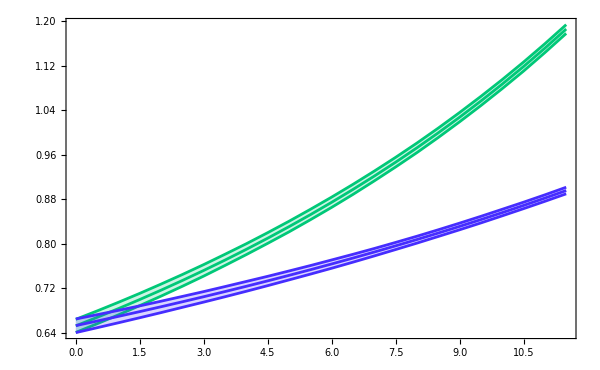

```mathematica
magni=1.6;
Show[
PlotEOSGGfit["BD","f+",1000,PlotStyle->{myGreen,myGreen,myGreen}],
PlotEOSGGfit["BD","f0",1000],
FrameLabel->{
MaTeX["q^2\\ [{\\rm GeV}^2]",Magnification->magni],
MaTeX["f_+^{BD} \\text{ and }f_0^{BD}",Magnification->magni]
}
]
```

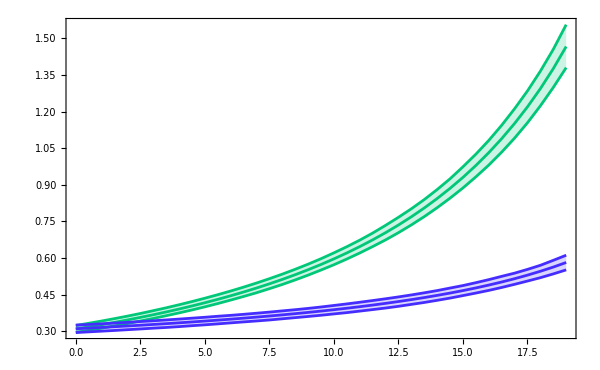

```mathematica
magni=1.6;
Show[
PlotEOSGGfit["BK*","T1",1000,PlotStyle->{myGreen,myGreen,myGreen}],
PlotEOSGGfit["BK*","T2",1000],
FrameLabel->{
MaTeX["q^2\\ [{\\rm GeV}^2]",Magnification->magni],
MaTeX["T_1^{BK^*} \\text{ and }T_2^{BK^*}",Magnification->magni]
}
]
```

B->P

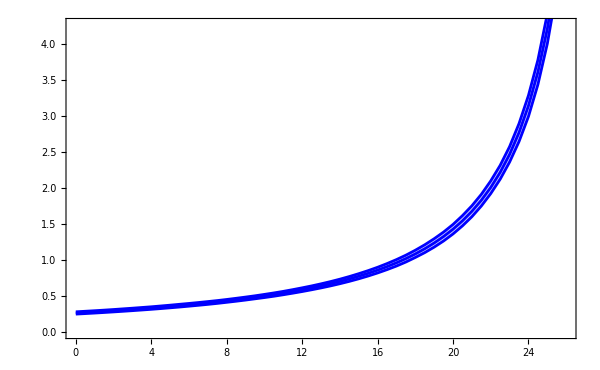

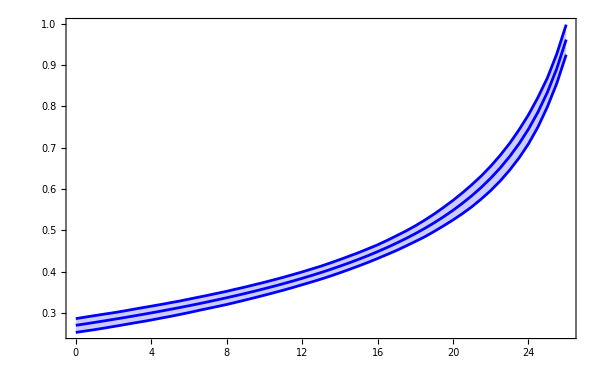

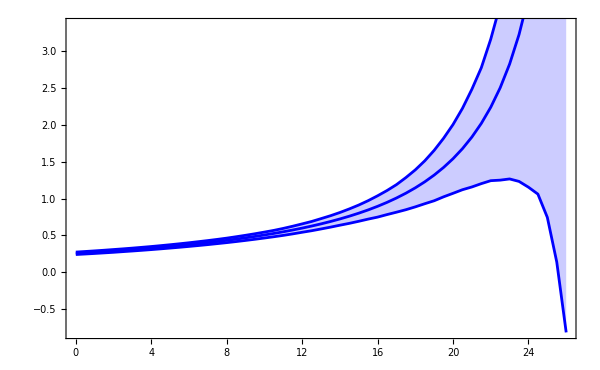

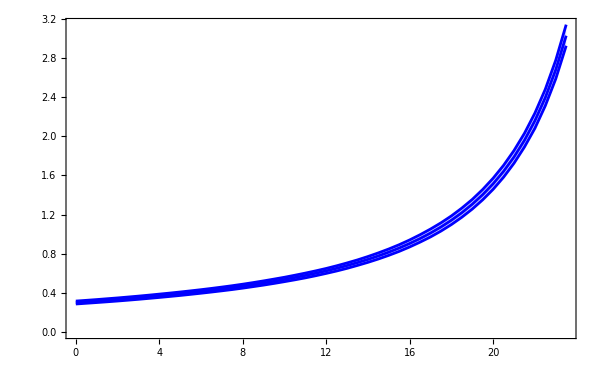

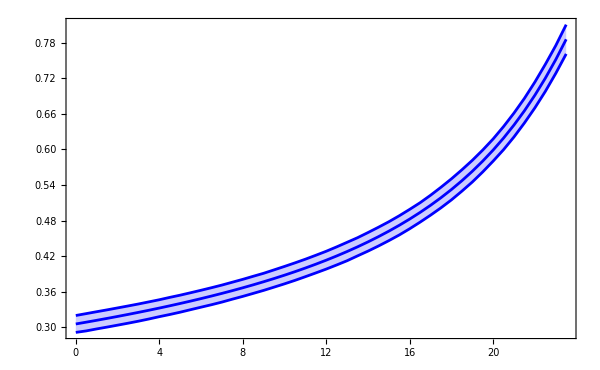

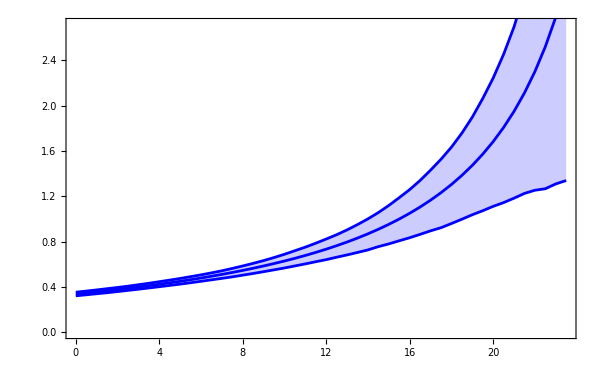

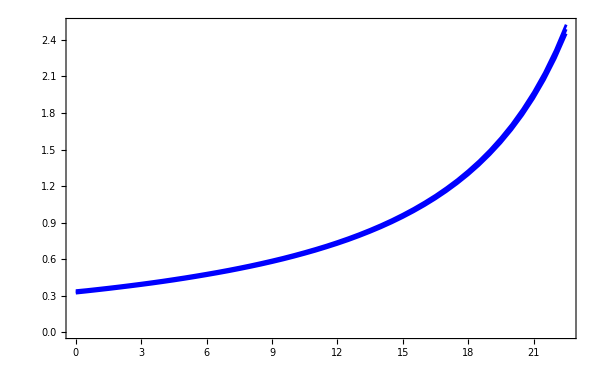

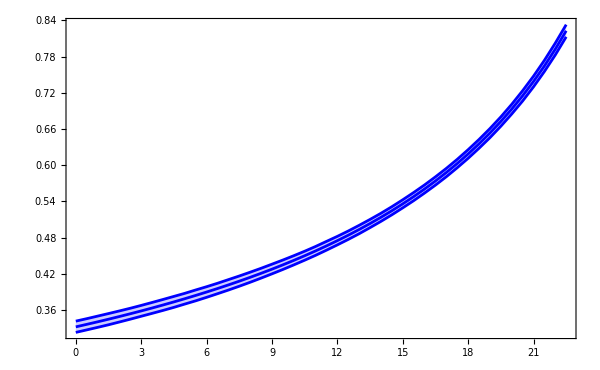

```mathematica
Do[
Print[PlotEOSGGfit[Mm,ff,1000]]
,{Mm,listMmP},{ff,listffP}]
```

B->V

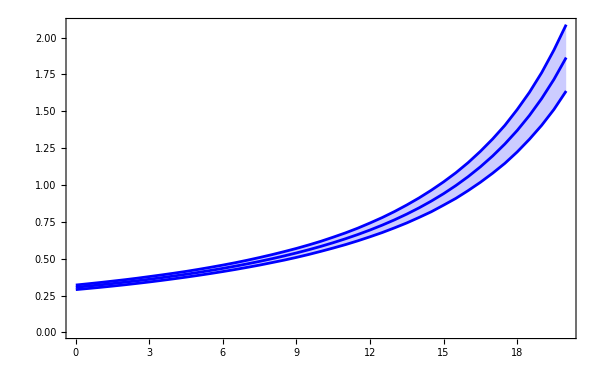

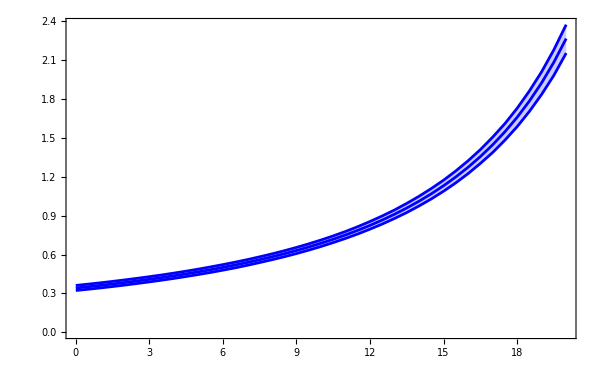

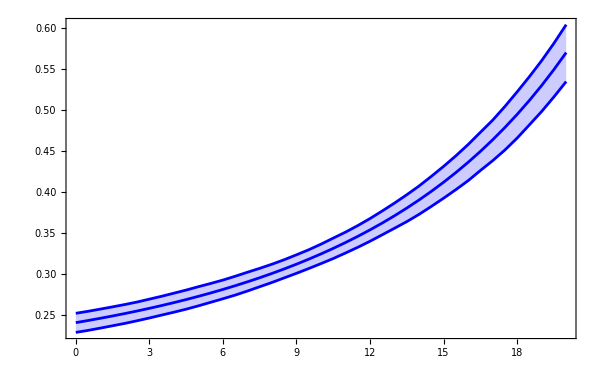

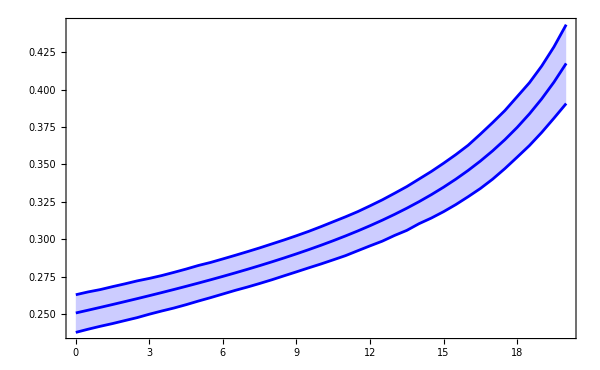

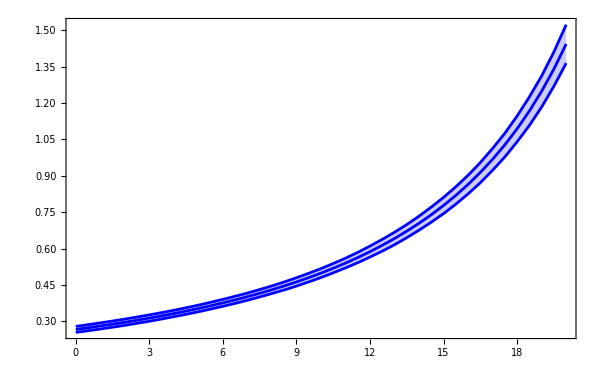

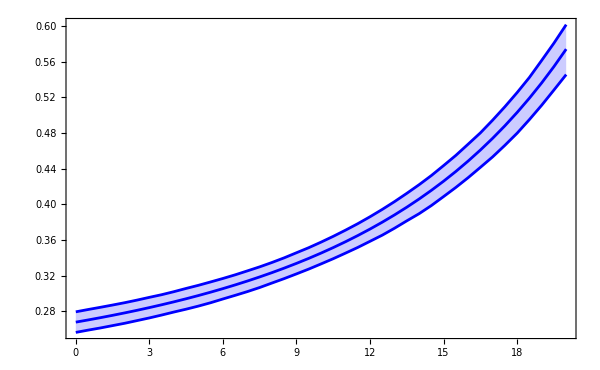

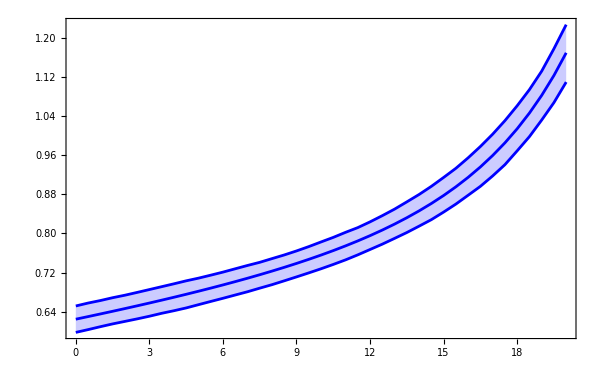

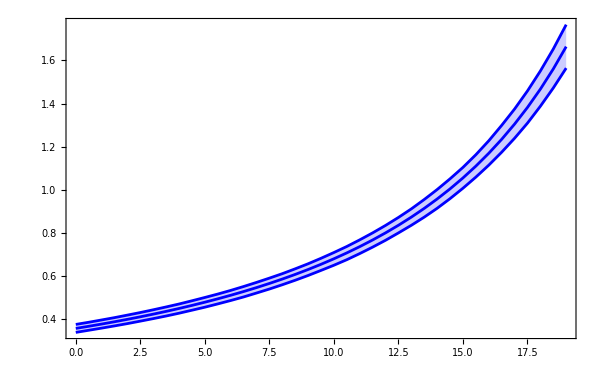

```mathematica
Do[
Print[PlotEOSGGfit[Mm,ff,1000]]
,{Mm,listMmV},{ff,listffV}]
```